```mathematica
ListLinePlot[Map[f, {{0.0000147,0.0000477, 0.0001327, 0.001386, 0.0053872, 0.0289211, 0.2540005, 2.1505047},{0.0052673, 0.0048508, 0.0025569, 0.00762, 0.0201786, 0.1201408, 1.4117979, 11.3463882}}], ScalingFunctions->{"Log", "Log"}, PlotLabels->{"xHBNN", "CMMA"}, PlotTheme->"Scientific", AspectRatio->0.5]
```

-Graphics-

```mathematica
{0.0000101,0.0000227, 0.0241061, 0.0234587, 0.0248575 ,0.0352349, 0.129645, 0.9212241}
```

```mathematica
{0.0052673, 0.0048508, 0.0025569, 0.00762, 0.0201786, 0.1201408, 1.4117979, 11.3463882}
```

```mathematica
f[x_] := Transpose[{{64, 128, 256, 512, 1024, 2048, 4096, 8192},x}];
```

```mathematica
Transpose[{{0.0000147,0.0000477, 0.0001327, 0.001386, 0.0053872, 0.0289211, 0.2540005, 2.1505047}, {64, 128, 256, 512, 1024, 2048, 4096, 8192}}]
```

{{0.0000147,64},{0.0000477,128},{0.0001327,256},{0.001386,512},{0.0053872,1024},{0.0289211,2048},{0.254001,4096},{2.1505,8192}}

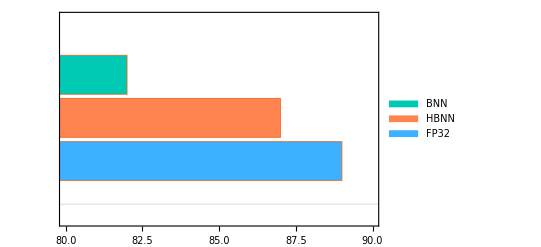

```mathematica
BarChart[{89, 87, 82}, PlotTheme->"Scientific", ChartStyle->96, BarOrigin->Left, ChartLegends->{"FP32", "HBNN", "BNN"}, PlotRange->{80,90}]
```

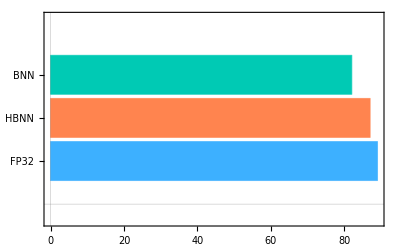

```mathematica
hiddennodes1 = 128; hiddennodes2 = 128; outputnodes=10;
```

```mathematica
mininet = NetGraph[{LinearLayer[hiddennodes1], Ramp,LinearLayer[hiddennodes2], Ramp, LinearLayer[outputnodes], LogisticSigmoid},{1->2->3->4->5->6}]
```

NetGraph[<>]